# Report Project II

Course code: IX1500
Date: 2018-10-04

Michel Ouadria, ouadria@kth.se
Rikard Jakobsson, rikjak@kth.se

Task 1: Probability Experiment

## Summary

### Task

Professor Alice is sending a message to the student Bob according to the procedure in section Section.Subsection.4. You are supposed to crack the message. When translating to ASCII, you can assume the base 256.

```mathematica
nBob=126456119090476383371855906671054993650778797793018127;
eBob=7937;
```

```mathematica
cipher={60833078379832053733665235104517667174744887177103669,47845135110330425759238983903835414959478333031403660,29226436027122547212719862444995325439654173683124719,26852073219160460393476539289841435348076003235573562,18536789208272843521201394019815486297145984481554371,60946204295190537657611153931568067486237180585452998,23651682987715782801807742133012602969829495021520007,112630050746349041975951827486336529408641182025699787,46387928110260904731968713144311859620686048715174256,101614383351383083936620333816943396668613455381224570};
```

The numbers is the list seems to be of the same size. Why?

### Result

●Straight Flush:
	• 256
	• Probability: 0.0149506%

●Straight:
	• 65 280
	• Probability: 3.81241%

●Full House:
	• 47 040
	• Probability: 2.74718%
	
●Five of a kind:
	• 336
	• Probability: 0.0196227%
	
●Four of a kind:
	• 16 800
	• Probability: 0.981134%
	
●Flush:
	• 2912
	• Probability: 0.170063%
	
●Three of a kind:
	• 215 040
	• Probability: 12.5585%
	
●Two pairs:
	• 37 5840
	• Probability: 21.9494%
	
●One pair:
	• 85 8240
	• Probability: 50.1219%
	
●Nothing:
	 • 130 560
	 • Probability: 7.62481%

### Discussion

For this discussion we assume the reader knows the probabilities for getting hands in a standard poker game.
In this variant of poker there is an increased chance of getting a point giving hand since there is a much smaller spread in the value of the cards (6 values compared to 14 values), as well as having a lot more duplicates due to mixing two decks of cards. We can see this clearly if we look at the probabilities calculated in this project and the probabilities from a standard take 5 poker game. 

Ours had a higher probability for all hands except flush, which is explained by it being covered by other hands. The best example of this is the four of a kind. In regular poker it is a very rare hand, since there are only four of each value, but in this game we get a probability about 40 times greater than that. 


●Straight Flush:
	-The probability of getting a straight flush is about 10 times greater than usual. This is because we have duplicates of each suite and there are fewer values to choose from.

●Straight:
	 -The probability of getting a straight is a bit less than 10 times greater than usual. This is because there are fewer values to choose from.

●Full House:
	 -Getting a Full house is about 19 times more likely. This is because there is a much greater chance of getting pairs and threes.
	 
	
●Five of a kind:
	-This is about an infinite amount more probable because it is impossible to get in regular poker.
	
●Four of a kind:
	-This is the hand that has seen the highest increase compared to the regular game. There is as mentioned about 40 times more likely since there are many more cards to choose from.
	
●Flush:
	-This is the only point giving hand that has seen a decrease compared to regular poker. This is due to the fact that it will be outranked by more hands and therefor a lot of flushes will be covered by other more valuable hands. There are also fewer cards in each suit, 12 compared to 13, which makes it less likely to get a flush.
	
●Three of a kind:
	-This is about 6 times more likely than usual. This is due to the fact that there are 8 of each value instead of 4.
	
●Two pairs:
	-This is about 5 times more likely than usual. This is as in most cases due to the fact that we have more cards of each value and there are fewer values to choose from. 
	
●One pair:
	-This is the hand that has seen the smallest increase. This is for the same reason as the flush mentioned above, ie a lot of hands containing a pair also contains something else to make it more valuable.
	
●Nothing:
	-This is a lot less common due to the fact that the possibility of a point giving hand is much higher.
For this discussion we assume the reader knows the probabilities for getting hands in a standard poker game.

## Code

```mathematica
deck = {109,109,110,110,111,111,112,112,113,113,114,114,209,209,210,210,211,211,212,212,213,213,214,214,309, 309,310,310,311,
311,312,312,313,313,314,314,409,409,410,410,411,411,412,412,
413,413,414,414};

hand = Subsets[deck,{5}](*Sort deck with all subsets containing 5*)
sizeOfPermutations = Length[hand] (*Amount of different possible hands*)
```

{{109,109,110,110,111},{109,109,110,110,111},{109,109,110,110,112},{109,109,110,110,112},{109,109,110,110,113},{109,109,110,110,113},{109,109,110,110,114},{109,109,110,110,114},{109,109,110,110,209},{109,109,110,110,209},{109,109,110,110,210},{109,109,110,110,210},{109,109,110,110,211},{109,109,110,110,211},{109,109,110,110,212},{109,109,110,110,212},{109,109,110,110,213},{109,109,110,110,213},{109,109,110,110,214},{109,109,110,110,214},{109,109,110,110,309},1712263,{411,412,412,413,414},{411,412,412,413,414},{411,412,412,413,414},{411,412,412,413,414},{411,412,412,414,414},{411,412,413,413,414},{411,412,413,413,414},{411,412,413,414,414},{411,412,413,414,414},{411,412,413,413,414},{411,412,413,413,414},{411,412,413,414,414},{411,412,413,414,414},{411,413,413,414,414},{412,412,413,413,414},{412,412,413,413,414},{412,412,413,414,414},{412,412,413,414,414},{412,413,413,414,414},{412,413,413,414,414}}
 |  |  |  |

1712304

#### Straight flush

```mathematica
straightFlushQ[h_]:=MatchQ[h-h[[1]],{0,1,2,3,4}](*subtracts the first value from the rest and then checks if they are in ascending order*)
straightFlush =Count[hand, _?(straightFlushQ)]
N[straightFlush/sizeOfPermutations]*100
```

256

0.0149506

#### Straight

```mathematica
straightQ[{9,10,11,12,13}]:=True;(*All possible hands from 9 to K = True*)
straightQ[{10,11,12,13,14}]:=True;(*All possible hands from 10 to A = True *)
straightQ[{___}]:=False(*All other possibilities = False*)
straightRemoveSuiteQ[hand_]:= straightQ[Sort[Mod[hand,100]]]; (*Calculating suites by removing the first digit from all cards in the deck, i.e 109 = 9 ...*)
straight =(Count[hand,_?(straightRemoveSuiteQ)]-straightFlush) (*Final result of all the chances of getting straight. Subtract Straight flush since the cases above doesn't exclude it as a possibility*)
N[(straight)/sizeOfPermutations]*100 (*Probability*)
```

65280

3.81241

#### Full house

```mathematica
fullHouseQ[{x_,x_,x_,y_,y_}/;x≠y]:=True;(*Check for three of a kind and a pair, they can't be the same rank*)
fullHouseQ[{x_,x_,y_,y_,y_}/;x≠y]:=True;(*Second scenario*)
fullHouseQ[___]:=False;(*Everything else is excluded*)
fullHouseRemoveSuiteQ[hand_]:=fullHouseQ[Sort[Mod[hand,100]]]
fullHouse =Count[hand,_?(fullHouseRemoveSuiteQ)]
N[fullHouse/sizeOfPermutations]*100
```

47040

2.74718

#### Five of a kind

```mathematica
fiveOfAKindQ[{x_,x_,x_,x_,x_}]:=True;(*Check for five of a kind*)
fiveOfAKindQ[{___}]:=False;(*Exclude everything else*)
fiveOfAKindRemoveSuiteQ[hand_]:=fiveOfAKindQ[Sort[Mod[hand,100]]]
fioak = Count[hand,_?(fiveOfAKindRemoveSuiteQ)]
N[fioak/sizeOfPermutations]*100
```

336

0.0196227

#### Four of a kind

```mathematica
fourOfAKindQ[{x_,x_,x_,x_,y_}/;x≠y]:=True; (*Checks for four of a kind*)
fourOfAKindQ[{y_,x_,x_,x_,x_}/;x≠y]:=True; 
fourOfAKindQ[{___}]:=False;
fourOfAKindRemoveSuiteQ[hand_]:=fourOfAKindQ[Sort[Mod[hand,100]]];
foak = Count[hand,_?(fourOfAKindRemoveSuiteQ)]
N[foak/sizeOfPermutations]*100
```

16800

0.981134

#### Flush

```mathematica
flushQ[h_]:=MatchQ[(h-h[[1] ]),{0,0,0,0,0}](*Removes the value and only keeps the suit. Makes sure that all have the same suite by removeing the suite from the first one and checking if  htey are all zeor*)
flushGetSuiteQ[hand_]:= flushQ[Quotient[hand,100]](*Get the suite through quotienet function. I.e 109 = 1*)
flush=Count[hand,_?(flushGetSuiteQ)]- straightFlush
N[flush/sizeOfPermutations]*100
```

2912

0.170063

#### Three of a kind

```mathematica
threeOfAKindQ[{___,x_,x_,x_,x_,___}]:=False; (*Four of a kind excluded*)
threeOfAKindQ[{x_,x_,y_,y_,y_}/;x≠y]:=False;(*Full house excluded*)
threeOfAKindQ[{x_,x_,x_,y_,y_}/;x≠y]:=False;(*Second scenario of full house*)
threeOfAKindQ[{___,x_,x_,x_,___}]:=True; (*Three of a kind*)
threeOfAKindQ[{___}]:=False; 
threeOfAKindRemoveSuiteQ[hand_]:=threeOfAKindQ[Sort[Mod[hand,100]]];
threePair =Count[hand,_?(threeOfAKindRemoveSuiteQ)]
N[threePair/sizeOfPermutations]*100
```

215040

12.5585

#### Two Pair Flush

```mathematica
twoPairQ[{x_,x_,y_,y_,z_}/;x≠y≠z]:=True;(*Two pair*)
twoPairQ[{z_,x_,x_,y_,y_}/;x≠y≠z]:=True;(*Second scenario*)
twoPairQ[{x_,x_,z_,y_,y_}/;x≠y≠z]:=True;(*Third senario*)
twoPairQ[{___}]:=False;
twoPairRemoveSuiteQ[hand_]:=twoPairQ[Sort[Mod[hand,100]]];
(*Check when a hand with two pair without suite are the same as the flush suite*)
twoPairWithFlushQ[hand_]:=twoPairRemoveSuiteQ[hand]&&flushGetSuiteQ[hand]
twoPairwithFlush = Count[hand,_?(twoPairWithFlushQ)]
```

480

#### Two pair

```mathematica
(*Go through all possible cases of twoPair excl. suite and exclude cases where two pair are of the same suite*)
twoPair = Count[hand,_?(twoPairRemoveSuiteQ)]-twoPairwithFlush

N[twoPair/sizeOfPermutations]*100
```

375840

21.9494

#### One pair

```mathematica
pairQ[{x_,x_,y_,z_,w_}/;x≠y≠z≠w]:=True;(* First case of two pairs *)
pairQ[{y_,x_,x_,z_,w_}/;x≠y≠z≠w]:=True;(*Second case*)
pairQ[{y_,z_,x_,x_,w_}/;x≠y≠z≠w]:=True;(*Third case*)
pairQ[{y_,z_,w_,x_,x_}/;x≠y≠z≠w]:=True;(*Fourth case*)
pairQ[{___}]:=False (* else *)

pairRemoveSuiteQ[hand_]:=pairQ[Sort[Mod[hand,100]]]
pairWithFlushQ[hand_]:=pairRemoveSuiteQ[hand]&&flushGetSuiteQ[hand]
pairWithFlush = Count[hand,_?(pairWithFlushQ)];
onePair = Count[hand,_?(pairRemoveSuiteQ)]-pairWithFlush
N[onePair/sizeOfPermutations]*100
```

858240

50.1219

#### Nothing

```mathematica
noHand = Length[hand] -straightFlush - straight-flush-fullHouse-foak-threePair-fioak-twoPair-onePair
N[noHand/sizeOfPermutations]*100
```

130560

7.62481

Task 2: Combinatorial Calculus & Monte Carlo Experiment

## Summary

### Task

Consider the following C of the probability of getting four of a kind. In this case we are dealing with sampling without replacement and without regard to order. First choose one of six possibilities {9,…,A} to be the kind value x, then we choose four out of the eight x and finally we add a last card from the remaining 40. The multiplication principle gives the result.

### Result

●Straight Flush:  2^5 Binomial[2, 1] Binomial[4, 1] = 256
Probability: 0.0149506%

●Straight: Binomial[2, 1] Binomial[8, 1]^5- Straight Flush = 65 280
Probability: 3.81241%

●Full House: Binomial[6, 1] Binomial[8, 3]Binomial[5, 1]Binomial[8, 2] = 47 040
Probability: 2.74718%

●Flush: Binomial[12, 5] Binomial[4, 1] - Straight Flush = 2912
Probability: 0.170063%

●Four of a kind: Binomial[6, 1] Binomial[8, 4]Binomial[40, 1] = 16 800
Probability: 0.981134%

●Three of a kind: Binomial[6, 1] Binomial[8, 3]Binomial[5, 2]Binomial[8, 1]^2 = 215 040
Probability: 12.5585%

### Discussion

The combinatorial method was more straightforward than the census method since  there weren’t any need hard syntax to deal with. Instead, we used logic and combinatorics to solve the probability. Some of the hands, such as flush and straight, required some extra thought since they need to exclude some cases.

We started task one with some combinatorics to understand the poker hands, this is likely why task two was more clearcut. Also due to the lack of hands to calculate.

### Conclusion

The result from the combinatorial calculations verifies the same probability as the census method.

## Code

### Deck

```mathematica
deckC=Binomial[48, 5]
```

1712304

### Straight Flush

The straight flush can start with possible cards, nine or ten, and can be of four possible suites. There are 2 choices for each spot.

```mathematica
straightFlushC=2^5 Binomial[2, 1] Binomial[4, 1]
```

256

```mathematica
N[(2^5 Binomial[2, 1] Binomial[4, 1])/deckC]*100
```

0.0149506

### Straight

The straight applies same principle above with the exception of flush, no sequence of five suites. 
Binomial[2, 1] = Two possible starting cards, pick one. Binomial[8, 1]=Eight possible values, including recurrence of same suite, pick one. Repeat five times. Exclude the possibility of flush and straight appearing together.

```mathematica
straightC=Binomial[2, 1] Binomial[8, 1]^5;
straightC - straightFlushC
```

```mathematica
N[(Binomial[2, 1] Binomial[8, 1]^5-2^5 Binomial[2, 1] Binomial[4, 1])/deckC]*100
```

3.81241

### Full House

The full house consists of three of kind and a pair of two in the same hand.
Binomial[6, 1]=Pick one out of six possible ranks.Binomial[8, 3]=Pick three out of eight possible values, including recurrence of same suite.Binomial[5, 1]=Pick one out of the remaining five cards.Binomial[8, 2]=Pick two out of eight possible suites, including recurrence of same suite.

```mathematica
fullHouseC=Binomial[6, 1] Binomial[8, 3]Binomial[5, 1]Binomial[8, 2]
```

47040

```mathematica
N[(Binomial[6, 1] Binomial[8, 3]Binomial[5, 1]Binomial[8, 2])/deckC]*100
```

2.74718

### Flush

The flush consists of a hand with hand of where all cards holds same suite, but not pair or straight of the rank.
Binomial[12, 5]=Pick five out of the 12 possible cards in a suiteBinomial[4, 1]=Pick a suite. Exclude all straight flushes.

```mathematica
flushC=Binomial[12, 5] Binomial[4, 1] ;
flushC-straightFlushC
```

```mathematica
N[(Binomial[12, 5] Binomial[4, 1]- 2^5 Binomial[2, 1] Binomial[4, 1])/deckC]*100
```

0.170063

### Four of a kind

This was given to us in the problem

```mathematica
fourOfAKindC=Binomial[6, 1] Binomial[8, 4]Binomial[40, 1]
```

```mathematica
N[(Binomial[6, 1] Binomial[8, 4]Binomial[40, 1])/deckC]*100
```

0.981134

### Three of a kind

There are 6 possible values, 8 cards of each value, then we pick 2 values of the remaining 5. We chose one of the 8 of these values.

```mathematica
threeOfAKindC=Binomial[6, 1] Binomial[8, 3]Binomial[5, 2] Binomial[8, 1]^2
```

```mathematica
N[(Binomial[6, 1] Binomial[8, 3]Binomial[5, 2] Binomial[8, 1]^2)/deckC]*100
```

12.5585

## Summary

### Task

Estimate the probability of one pair using the Monte Carlo method. Draw a diagram that shows how the probability estimate stabilises with increasing sample size.

### Result

This is the graph acquired from running our Monte Carlo simulation a 1000 times.

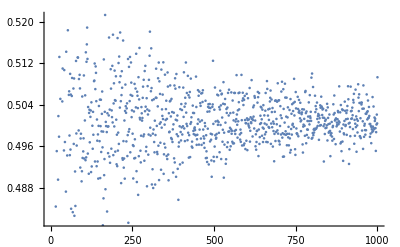

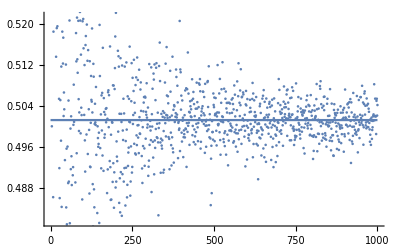

### Discussion

There were some performance issues with iterating more than 1000 since Mathematica runs rather slow on our systems. The scatter plot along with the line gives a clear presentation 
that probability goes towards the same estimate of one pair in task one.

### Conclusion

We clearly see that it converges towards 0.5, which is very close to the number we calculated in the probability experiment.

## Code

```mathematica
monteCarlo[h_]:=(counter = 0;
For[i=1,i≤h,i++,
chosenHand = RandomChoice[hand];
If[(pairRemoveSuiteQ[chosenHand]&&Not[pairWithFlushQ[chosenHand]]),counter++]
];
N[counter/h])

array=Range[1000];
(*Run monte carlo 1000 times*)
For[j=1, j<=1000,j++,
array[[j]] = monteCarlo[j^1.5];
];
array(*Print array*)
```

{1.,0.707107,0.3849,0.5,0.536656,0.204124,0.647939,0.486136,0.518519,0.695701,0.438562,0.673575,0.362689,0.477252,0.464758,0.609375,0.513605,0.589256,0.519204,0.458394,0.519566,0.523311,0.543951,0.467784,0.536,0.505376,0.491817,0.485954,0.435424,0.505122,0.446116,0.497184,0.511683,0.484231,0.478116,0.518519,0.528743,0.512278,0.517337,0.502012,0.506612,0.503323,0.464589,0.493382,0.526718,0.528868,0.512079,0.484132,0.495627,0.480833,0.472251,0.49603,0.528709,0.48889,0.505037,0.489184,0.476367,0.520698,0.481037,0.563734,0.499554,0.491613,0.501953,0.494141,0.488506,0.479311,0.536087,0.490421,0.492012,0.500289,0.508143,0.500867,0.52909,0.524685,0.549637,0.489018,0.470642,0.518234,0.512698,0.49473,0.521262,0.513103,0.51047,0.544246,0.520633,0.505309,0.499087,0.502718,0.522853,0.522361,0.520687,0.498621,0.514016,0.503641,0.502189,0.469911,0.485691,0.520538,0.532975,0.521,0.515252,0.47663,0.502231,0.511976,0.497244,0.491141,0.515894,0.517655,0.478913,0.498401,0.519899,0.523076,0.512818,0.494583,0.514905,0.549082,0.503339,0.499295,0.486852,0.512729,0.492111,0.49201,0.500683,0.509847,0.505172,0.504827,0.519138,0.502709,0.488684,0.480358,0.512217,0.509705,0.487668,0.484153,0.50046,0.504408,0.500766,0.500267,0.507693,0.494415,0.53396,0.537194,0.483032,0.5,0.4977,0.495997,0.496555,0.498751,0.481093,0.519836,0.50983,0.495736,0.47873,0.502331,0.491778,0.506046,0.499186,0.506538,0.494286,0.515352,0.524265,0.491289,0.505515,0.502803,0.497768,0.49842,0.50229,0.524448,0.503414,0.500783,0.503552,0.527095,0.486935,0.501477,0.49157,0.506659,0.507043,0.499828,0.506085,0.479512,0.493202,0.515616,0.492006,0.485597,0.498356,0.48567,0.530661,0.500829,0.500708,0.489124,0.508018,0.492777,0.507974,0.484067,0.490998,0.507289,0.511387,0.517568,0.488024,0.522198,0.48918,0.497046,0.49407,0.493187,0.477317,0.514771,0.498957,0.513698,0.51167,0.485018,0.502455,0.489833,0.483171,0.513328,0.491036,0.502435,0.500843,0.482488,0.511894,0.490634,0.499178,0.497321,0.50539,0.489184,0.502519,0.491829,0.511681,0.4784,0.484504,0.497116,0.491897,0.512491,0.499355,0.4861,0.488552,0.505861,0.492248,0.494868,0.495825,0.505371,0.500892,0.515588,0.500793,0.486435,0.489197,0.496066,0.504906,0.512353,0.490945,0.49205,0.509482,0.500453,0.50221,0.506905,0.513013,0.496582,0.504609,0.502643,0.494697,0.508065,0.494476,0.509569,0.498225,0.496329,0.513458,0.500193,0.509075,0.497795,0.500235,0.494754,0.511071,0.50179,0.498592,0.498511,0.507197,0.508587,0.503015,0.501166,0.494183,0.491751,0.488916,0.499833,0.496135,0.50292,0.50464,0.505717,0.495672,0.492274,0.505801,0.505617,0.497574,0.502836,0.502258,0.508426,0.501698,0.499747,0.500351,0.503666,0.49031,0.492095,0.493283,0.512176,0.49637,0.49996,0.50107,0.499177,0.497297,0.511528,0.487138,0.502371,0.49995,0.507347,0.496972,0.493881,0.510312,0.509138,0.490607,0.512101,0.497234,0.495778,0.505113,0.499474,0.511454,0.512346,0.497865,0.500503,0.497701,0.502665,0.496856,0.482589,0.499666,0.511792,0.500602,0.516377,0.508847,0.496835,0.490908,0.497582,0.502431,0.496228,0.495635,0.497258,0.501854,0.502958,0.490942,0.49907,0.491499,0.50263,0.501698,0.50856,0.50061,0.512257,0.49802,0.502217,0.515495,0.50603,0.502126,0.501648,0.505875,0.5045,0.497886,0.501196,0.497536,0.4916,0.50177,0.510855,0.506777,0.498763,0.496314,0.492336,0.502102,0.497848,0.513616,0.495658,0.494916,0.503229,0.492895,0.504139,0.503907,0.500839,0.501155,0.501867,0.502571,0.511108,0.509647,0.501734,0.502286,0.507935,0.504674,0.493775,0.500677,0.500953,0.499299,0.499573,0.520606,0.495159,0.511114,0.510575,0.503261,0.506,0.498754,0.497018,0.505057,0.50109,0.501689,0.493969,0.497874,0.499199,0.498458,0.502176,0.497824,0.507014,0.499574,0.499427,0.507441,0.492058,0.500624,0.507253,0.498909,0.514439,0.500104,0.506403,0.5007,0.502824,0.496371,0.502699,0.504901,0.503923,0.501937,0.503327,0.5018,0.50507,0.509204,0.498265,0.500075,0.505385,0.506716,0.496909,0.504345,0.499376,0.501998,0.498035,0.496457,0.503439,0.498866,0.500481,0.508537,0.50346,0.504722,0.499794,0.497088,0.500642,0.503757,0.508399,0.501572,0.508139,0.509236,0.506855,0.49564,0.496964,0.502117,0.502905,0.503484,0.500957,0.50393,0.506782,0.50674,0.502549,0.50045,0.505724,0.502157,0.494809,0.508308,0.500111,0.500947,0.495999,0.501256,0.500162,0.499073,0.50864,0.508856,0.503777,0.499387,0.511739,0.500233,0.49785,0.502366,0.501286,0.497622,0.484575,0.493666,0.496193,0.486919,0.501016,0.498862,0.498894,0.497389,0.506419,0.50418,0.503741,0.505623,0.497089,0.502167,0.502441,0.505531,0.502452,0.499126,0.496256,0.501935,0.502717,0.511976,0.500378,0.500207,0.500464,0.502686,0.50643,0.498836,0.509268,0.497309,0.494441,0.501007,0.504599,0.507249,0.500963,0.501943,0.512532,0.501816,0.500803,0.497493,0.496905,0.507353,0.49867,0.496129,0.499031,0.505391,0.506797,0.494454,0.503493,0.50457,0.502691,0.498357,0.504587,0.492366,0.501019,0.497204,0.504617,0.499169,0.502559,0.504451,0.500518,0.499233,0.500113,0.499065,0.50523,0.502641,0.49976,0.50549,0.504359,0.496802,0.50332,0.497083,0.507991,0.498853,0.506187,0.50194,0.499348,0.496027,0.498633,0.500266,0.503139,0.50878,0.49502,0.49861,0.505888,0.512329,0.497468,0.499206,0.504603,0.502005,0.507007,0.504128,0.511162,0.499334,0.496564,0.50568,0.505796,0.499934,0.501534,0.506624,0.506243,0.501131,0.50007,0.497975,0.502244,0.499118,0.492158,0.50429,0.506923,0.504085,0.500104,0.493495,0.505332,0.501104,0.499725,0.497681,0.498393,0.498299,0.497203,0.502766,0.505181,0.50361,0.500461,0.502861,0.499201,0.498639,0.499453,0.505352,0.508487,0.493944,0.506417,0.496535,0.499915,0.505078,0.502004,0.502784,0.500814,0.501845,0.502108,0.505729,0.496557,0.498721,0.499174,0.500441,0.49625,0.489642,0.499086,0.500586,0.500465,0.497804,0.503926,0.504411,0.497639,0.502612,0.499789,0.494293,0.49948,0.498383,0.505414,0.499226,0.50598,0.495663,0.507077,0.501598,0.493931,0.50479,0.501732,0.500349,0.496365,0.493049,0.505435,0.502228,0.499917,0.503648,0.501225,0.501786,0.499725,0.498544,0.50229,0.504401,0.504771,0.500594,0.503782,0.501056,0.497941,0.493414,0.499772,0.504059,0.50521,0.495955,0.500275,0.497598,0.492013,0.501577,0.505453,0.500999,0.500071,0.502923,0.498391,0.492994,0.498157,0.49625,0.499734,0.499311,0.494184,0.500814,0.504527,0.50067,0.509247,0.4969,0.50712,0.498977,0.502858,0.504146,0.50243,0.499224,0.498537,0.502586,0.503327,0.501627,0.500197,0.496189,0.500986,0.504817,0.507793,0.503695,0.501857,0.50237,0.504387,0.500638,0.503736,0.501552,0.506232,0.507034,0.49813,0.507192,0.501492,0.504641,0.503398,0.502108,0.502446,0.501769,0.497258,0.505512,0.501764,0.500188,0.497266,0.505601,0.502229,0.507631,0.50233,0.499579,0.506931,0.499933,0.499123,0.496348,0.499374,0.497343,0.498155,0.497792,0.501519,0.508389,0.498065,0.499299,0.501398,0.5018,0.502921,0.503893,0.505724,0.50066,0.499385,0.500307,0.499085,0.498388,0.4976,0.503477,0.505416,0.50278,0.499825,0.498944,0.502325,0.502096,0.503125,0.502801,0.495743,0.502663,0.499749,0.494675,0.503076,0.50151,0.5005,0.501188,0.50384,0.505112,0.501594,0.506001,0.500135,0.49959,0.500628,0.504189,0.501205,0.502907,0.503974,0.498229,0.498361,0.500276,0.506102,0.502794,0.499498,0.502059,0.498113,0.503135,0.501314,0.49361,0.497953,0.495186,0.498242,0.504077,0.503055,0.501601,0.5018,0.501998,0.497916,0.505323,0.508268,0.503336,0.495117,0.501146,0.49856,0.501274,0.503466,0.498508,0.49658,0.5008,0.507879,0.507336,0.508816,0.500031,0.50433,0.500862,0.497197,0.503646,0.498488,0.500544,0.497776,0.50401,0.505754,0.503155,0.5058,0.497571,0.498655,0.498216,0.500399,0.497384,0.496011,0.50079,0.504413,0.505386,0.5002,0.502025,0.499969,0.500739,0.500099,0.50207,0.497182,0.507269,0.500751,0.497802,0.4953,0.49952,0.504438,0.497108,0.498258,0.500903,0.498261,0.494292,0.494221,0.503198,0.504323,0.501657,0.502585,0.502304,0.500702,0.502129,0.498946,0.500022,0.495579,0.502625,0.498115,0.503251,0.500555,0.497409,0.495379,0.496977,0.500281,0.499851,0.499536,0.503916,0.502649,0.496708,0.500165,0.498458,0.499685,0.501394,0.502685,0.503225,0.501674,0.495029,0.503604,0.49846,0.498037,0.507191,0.501697,0.501675,0.500291,0.50027,0.502705,0.501325,0.504298,0.499963,0.504494,0.498609,0.503671,0.501901,0.504733,0.49733,0.500123,0.505319,0.501042,0.49283,0.504677,0.50271,0.497035,0.4999,0.496561,0.498138,0.506523,0.501841,0.499934,0.50114,0.502271,0.499315,0.498581,0.50171,0.500554,0.498912,0.498357,0.505927,0.501254,0.501914,0.494902,0.499171,0.499414,0.505147,0.500793,0.497692,0.500271,0.502258,0.505712,0.5057,0.501623,0.500627,0.501098,0.507924,0.502069,0.50023,0.504655,0.496399,0.499804,0.504343,0.506413,0.506831,0.502287,0.504015,0.50019,0.500747,0.499604,0.505447,0.504099,0.499871,0.500952,0.504409,0.499836,0.503447,0.502837,0.500651,0.49939,0.496986,0.498349,0.501405,0.496368,0.501109,0.501709,0.497537,0.499273,0.499807,0.501049,0.502029,0.50233,0.501954,0.508224,0.501173,0.502015,0.505412,0.502001,0.501913,0.498485,0.504978,0.505393,0.5021,0.504162}

```mathematica
aPlot = ListPlot[array];
probabilityPlot =Plot[0.501219409637541,{x,0,1000},PlotLabel->"0.501"];
Show[aPlot,probabilityPlot]
```

-Graphics-